{}

List

StringForm::sfr: Item 2 requested in "Delayed time `1` = `2` computed at `3` = `4` did not evaluate to a real number." out of range; 1 items available.

StringForm::sfr: Item 3 requested in "Delayed time `1` = `2` computed at `3` = `4` did not evaluate to a real number." out of range; 1 items available.

StringForm::sfr: Item 4 requested in "Delayed time `1` = `2` computed at `3` = `4` did not evaluate to a real number." out of range; 1 items available.

General::stop: Further output of StringForm::sfr will be suppressed during this calculation.

NDSolve::rdelay: Delayed time 0.-1. List = `2` computed at `3` = `4` did not evaluate to a real number.

ReplaceAll::reps: {NDSolve[{y'[t]==0.1 (-1+1/20 y[«1»]) y[t] (1-1/100 y[«1»]),y[0]==50},y,{t,0,30}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::rdelay: Delayed time 0.-1. List = `2` computed at `3` = `4` did not evaluate to a real number.

ReplaceAll::reps: {NDSolve[{y'[t]==0.1 (-1.+0.05 y[«1»]) y[t] (1.-0.01 y[«1»]),y[0.]==50.},y,{t,0.,30.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::rdelay: Delayed time 0.-1. List = `2` computed at `3` = `4` did not evaluate to a real number.

General::stop: Further output of NDSolve::rdelay will be suppressed during this calculation.

0.1

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

0.644444

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

1.18889

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of NDSolve::ihist will be suppressed during this calculation.

1.73333

2.27778

2.82222

3.36667

3.91111

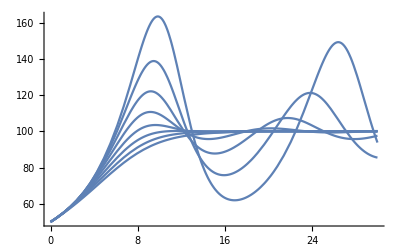

-Graphics-

```mathematica
Remove[T,A,K,r]
r=0.1;
K=100;
A=20;
T=5;
plt={}
Tlist = N@Subdivide[0.1,5,9];
For[i=0,i<9,i++,
T= Tlist[[i]];
Print[T];
s=NDSolve[{y'[t]==r*y[t]*(1-y[t-T]/K)*(y[t]/A-1) ,y[0]==50},y,{t,0,30}];
plt = {plt,Plot[Evaluate[y[x]/. s],{x,0,30},PlotRange->All]}
]


Show[plt]
```

2

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

InterpolatingFunction::dmval: Input value {-1.99939} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Failed

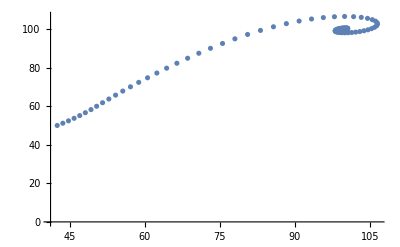

```mathematica
T=2
s=NDSolve[{y'[t]==r*y[t]*(1-y[t-T]/K)*(y[t]/A-1) ,y[0]==50},y,{t,0,30}];
Plot[Evaluate[y[x-T]/. s],{x,0,30},PlotRange->All];
time  = N@Subdivide[0,30,100];
ylist = y[time-T]/. s;
xlist = y[time]/. s;
ylist[[1]];
Plot[{1,2,3},{3,2,1}]
ListPlot[Transpose[{ylist[[1]],xlist[[1]]}]]
```